# Coulb 1 Behavior Analysis Tests

## SPP019 140813

```mathematica
<<NounouW`
```

HokahokaW`
(origin)[https://github.com/ktakagaki/HokahokaW.git]
current Git HEAD:  3d4110fc77f60ded9faaf750be6f7fbc171cbb75
newest file:  Tue 16 Sep 2014 00:26:42

NounouW`
(origin)[https://ktakagaki@github.com/ktakagaki/NounouW.git]
current Git HEAD:  1e2a8c3ff50e054011b26b77698774a3688a2ae1
newest file:  Tue 16 Sep 2014 00:26:56

<<Set JLink` java stack size to 6144Mb>>

```mathematica
coulb1Folder="U:\\VSDdata\\project.SPP\\SPP.Coulb1";
nlx2Folder="U:\\VSDdata\\project.SPP\\SPP.Nlx2";
subjectString="SPP019";
```

```mathematica
videoFile=FileNameJoin[{coulb1Folder,"_arch",subjectString,"2014-08-13 16-38-54.153.wmv"}]
```

U:\VSDdata\project.SPP\SPP.Coulb1\_arch\SPP019\2014-08-13 16-38-54.153.wmv

```mathematica
nlxNevFile=FileNameJoin[{nlx2Folder,"_arch",subjectString,"2014-08-13_16-26-29", "Events.nev"}]
```

U:\VSDdata\project.SPP\SPP.Nlx2\_arch\SPP019\2014-08-13_16-26-29\Events.nev

## Import Events

```mathematica
{eventObj}=NNDataReader`load[nlxNevFile]
```

{«JavaObject[nounou.data.XEvents]»}

```mathematica
{eventObj@lengths[], eventObj@ports[]}
```

{{2,100,465},{0,100000000,100000001}}

```mathematica
Methods[(eventObj@toArray[])[[1]]]
```

```mathematica
(events0={"Events", #@timestamp[], #@duration[], #@code[], #@comment[]}& /@eventObj@filterByPortA[0]) //TableForm
```

Events | -9223372036423655351 | 0 | 0 | Starting Recording
Events | -9223372034010724351 | 0 | 0 | Stopping Recording

```mathematica
(eventsStim={"Stimulus", #@timestamp[], #@duration[], #@code[], #@comment[]}& /@eventObj@filterByPortA[100000000]) //TableForm
```

Stimulus | -9223372036208297913 | 16718 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372036190838445 | 22969 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372036163035320 | 14344 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372036149573882 | 12250 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372036125068226 | 12531 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372036109253163 | 12812 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372036098028288 | 14031 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372036077698038 | 14031 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372036059219132 | 12219 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372036042178038 | 13125 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372036012722101 | 12844 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372035988331413 | 13437 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372035977318820 | 11625 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372035958930413 | 13437 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372035929717851 | 12844 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372035911540820 | 12532 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372035882221382 | 13125 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372035868550632 | 15812 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372035840493351 | 19094 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372035817269320 | 12219 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372035793033320 | 16719 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372035767010132 | 12531 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372035738829570 | 15532 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372035713206820 | 12532 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372035702592007 | 13156 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372035689787507 | 13156 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372035663976351 | 33750 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372035640876226 | 12531 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372035624097882 | 20312 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372035603849726 | 13406 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372035588542913 | 11625 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372035570313663 | 13437 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372035544548788 | 13125 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372035521793882 | 12531 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372035494151663 | 13125 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372035470205320 | 13438 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372035446536945 | 12844 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372035435187538 | 13125 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372035419677695 | 12563 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372035396087851 | 31938 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372035382597757 | 13125 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372035357278101 | 12250 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372035328150913 | 12531 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372035302802913 | 12250 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372035291413788 | 12531 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372035281080257 | 13437 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372035264456570 | 12219 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372035239936288 | 12812 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372035226042476 | 24781 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372035200801663 | 12250 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372035173135288 | 12812 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372035152167226 | 16125 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372035141681382 | 12531 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372035113588288 | 11937 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372035091022070 | 12813 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372035068849726 | 13438 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372035046556445 | 13750 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372035019409320 | 12844 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372034991558976 | 14906 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372034961639913 | 11937 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372034938479476 | 12844 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372034922228476 | 15813 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372034892827163 | 19375 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372034863955320 | 14344 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372034841874320 | 13125 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372034829814257 | 12844 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372034806348351 | 18219 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372034783002195 | 12532 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372034763779476 | 14625 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372034744468945 | 13125 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372034732048757 | 12531 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372034712003663 | 12531 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372034697349007 | 12531 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372034682119538 | 12843 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372034659212913 | 16125 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372034648737820 | 12532 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372034627394382 | 14312 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372034604163195 | 14625 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372034584912101 | 13125 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372034556535007 | 12812 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372034540900632 | 14312 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372034524529882 | 12812 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372034501292101 | 17000 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372034479066320 | 12844 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372034468527351 | 13438 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372034453546913 | 12531 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372034434339101 | 13406 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372034404595320 | 12532 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372034383741007 | 13125 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372034354534101 | 12219 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372034330220757 | 20594 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372034301760976 | 20906 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372034285009788 | 12218 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372034268782663 | 13125 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372034250129695 | 13157 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372034231839507 | 13437 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372034218403726 | 12219 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372034192629007 | 15812 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
Stimulus | -9223372034172473726 | 11938 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
Stimulus | -9223372034150142538 | 12843 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).

```mathematica
(eventsCoulb={"Coulbourn", #@timestamp[], #@duration[], #@code[], #@comment[]}& /@eventObj@filterByPortA[100000001]) //TableForm
```

Coulbourn | -9223372036395363788 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372036322474070 | 0 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
Coulbourn | -9223372036322473945 | 0 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
Coulbourn | -9223372036273406757 | 0 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
Coulbourn | -9223372036208278632 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372036208278538 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372036204272757 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372036203822538 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372036203822445 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372036190823851 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372036190823757 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372036186820913 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372036186313570 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372036186313476 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372036163015288 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372036163015163 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372036159014382 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372036158574570 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372036158574476 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372036149559351 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372036145554445 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372036145554351 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372036145548695 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372036125054382 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372036121050538 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372036121050445 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372036121045007 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372036109240070 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372036109239976 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372036105235882 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372036104495632 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372036104495538 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372036098010351 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372036098010226 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372036094005538 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372036093755226 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372036093755101 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372036077681351 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372036077681257 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372036073675101 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372036073035601 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372036073035507 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372036059206288 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372036055201132 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372036055201070 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372036055195913 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372036042161320 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372036042161226 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372036038158132 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372036037801351 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372036037801257 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372036012707601 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372036012707476 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372036009187538 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372036009182288 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035988317757 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035984312320 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372035984312226 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372035984307413 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035977303413 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035973297851 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372035973297757 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372035973292913 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035958913601 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372035958913476 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372035954908570 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372035954348445 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035954348351 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035929704726 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035925869476 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372035925869382 | 0 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Coulbourn | -9223372035925234351 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372035925234226 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035911524976 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372035911524882 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372035907518632 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372035906329413 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035906329288 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035882205038 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035878201726 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372035878201632 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372035878199882 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035868535413 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035864530413 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372035864530320 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372035864525288 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035840471538 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035836466445 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372035836466351 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372035836461163 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035835521195 | 0 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
Coulbourn | -9223372035835521101 | 0 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
Coulbourn | -9223372035817256601 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372035817256507 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372035813251601 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372035812685601 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035812685507 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035793016820 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035789012726 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372035789012632 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372035789007507 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035766997757 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035762992820 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372035762992726 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372035762987632 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035738813976 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372035738813882 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372035734808695 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372035734282132 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035734282038 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035713194101 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035709188945 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372035709188882 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372035709183726 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035702579663 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372035702579570 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372035700649663 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372035700644351 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035689774226 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372035689774132 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372035685770101 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372035685275851 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035685275757 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035663959163 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372035663959070 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372035659954757 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372035659389976 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035659389851 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035640860351 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035636855320 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372035636855226 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372035636850132 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035624075570 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372035624075476 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372035620070757 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372035619265632 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035619265507 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035603836195 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035599831007 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372035599830945 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372035599823663 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035588526601 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372035588526507 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372035584521507 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372035584121320 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035584121226 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035570292726 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035566291726 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372035566291632 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372035566286476 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035544532913 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372035544532820 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372035541057976 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372035541052382 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035521778007 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035517773101 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372035517773007 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372035517767851 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035494139101 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372035494139007 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372035490134132 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372035489733913 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035489733820 | 0 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
Coulbourn | -9223372035489733788 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035470189257 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035466184257 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372035466184163 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372035466178851 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035446519476 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372035446519382 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372035443478726 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372035443474038 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035435175070 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035431170038 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372035431169976 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372035431164882 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035419660476 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372035419660382 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372035417450601 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372035417445320 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035396055445 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035392050695 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372035392050601 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372035392045413 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035382581038 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372035382580913 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372035378576101 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372035378075663 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035378075570 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035357261288 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372035357261163 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372035353257038 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372035352871507 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035352871413 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035328137226 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035324132351 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372035324132257 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372035324126976 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035302787351 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035298783382 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372035298783288 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372035298777945 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035291397507 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372035291397413 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372035287392945 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372035286550507 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035286550413 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035281063226 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035277058445 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372035277058382 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372035277053288 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035264444070 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372035264443976 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372035261328976 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372035261323695 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035239924070 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035235919101 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372035235919007 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372035235913882 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035226029695 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372035226029570 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372035222022820 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372035221449413 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035221449288 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035200784726 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372035200784632 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372035196780695 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372035196105507 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035196105413 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035173120632 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035169115726 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372035169115663 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372035169110507 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035152146101 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372035152146007 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372035148144226 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372035147715788 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035147715663 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035141666351 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372035141666257 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372035137661601 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372035137236320 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035137236226 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035113571632 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035109567507 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372035109567413 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372035109562382 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035091006601 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035087002695 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372035087002601 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372035086997007 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035068833007 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372035068832913 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372035064827195 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372035064207132 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035064207038 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035046543101 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035042538132 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372035042538038 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372035042532976 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372035019394288 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372035019394195 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372035015389257 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372035014708945 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372035014708851 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034991544226 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372034991544132 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372034987539351 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372034985535070 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034985534945 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034961625132 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372034961625038 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372034959795288 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372034959789945 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034938465288 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034934460445 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372034934460351 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372034934456163 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034922213382 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372034922213288 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372034918210788 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372034917521601 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034917521507 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034892804788 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034888801726 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372034888801632 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372034888796476 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034863937757 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372034863937632 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372034859932632 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372034859680538 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034859680445 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034841857882 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034837852913 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372034837852820 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372034837847445 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034829798632 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372034829798507 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372034825793445 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372034825193226 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034825193101 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034806328726 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034802323663 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372034802323570 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372034802318413 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034782988945 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034778983788 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372034778983726 | 0 | 11 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000B).
Coulbourn | -9223372034778983695 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372034778978538 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034763759351 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034759760195 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372034759760132 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372034759754945 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034759545070 | 0 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
Coulbourn | -9223372034744454570 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034744454476 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372034740450476 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372034739870288 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034739870163 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034732034976 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034728030007 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372034728029913 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372034728021820 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034711990320 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034707986226 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372034707986163 | 0 | 11 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000B).
Coulbourn | -9223372034707986132 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372034707981070 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034707046132 | 0 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
Coulbourn | -9223372034697335976 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034693330788 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372034693330695 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372034693325538 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034682106320 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372034682106195 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372034678101101 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372034677500976 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034677500851 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034659196570 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372034659196476 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372034655192101 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372034654751851 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034654751757 | 0 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
Coulbourn | -9223372034654751726 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034648722007 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034644716945 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372034644716851 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372034644711976 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034627377445 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372034627377351 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372034623372226 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372034622906945 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034622906851 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034604147538 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034600143476 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372034600143413 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372034600138163 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034584895163 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034580892788 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372034580892726 | 0 | 11 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000B).
Coulbourn | -9223372034580892695 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372034580888538 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034561638476 | 0 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
Coulbourn | -9223372034556518820 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034556518726 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372034552513757 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372034552158538 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034552158445 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034540882413 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034536878820 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372034536878726 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372034536873820 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034535374038 | 0 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
Coulbourn | -9223372034524514413 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034524514288 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372034520509570 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372034520079445 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034520079351 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034501279507 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034497275788 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372034497275695 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372034497270538 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034479050945 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034475045976 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372034475045882 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372034475040695 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034468510726 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372034468510632 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372034464505632 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372034463705351 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034463705257 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034453531007 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034449525976 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372034449525882 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372034449520882 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034434326445 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034430321257 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372034430321195 | 0 | 11 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000B).
Coulbourn | -9223372034430321163 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372034430316038 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034404582351 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034400577320 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372034400577226 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372034400572070 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034383727507 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372034383727413 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372034379722632 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372034379267382 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034379267288 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034354518663 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034350513445 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372034350513382 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372034350508320 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034330199820 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034326198695 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372034326198632 | 0 | 11 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000B).
Coulbourn | -9223372034326198601 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372034326193445 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034301739788 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372034301739695 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372034297734476 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372034297199288 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034297199163 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034284994820 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034280990070 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372034280989976 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372034280984788 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034268765507 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372034268765382 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372034264760476 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372034264300257 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034264300163 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034250115882 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034246114882 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372034246114788 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372034246110507 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034231825007 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372034231824913 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372034227821163 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372034227441038 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034227440945 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034218386663 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372034218386570 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372034214381570 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372034213931538 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034213931445 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034192611788 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034190586851 | 0 | 15 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000F).
Coulbourn | -9223372034190586757 | 0 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Coulbourn | -9223372034189871038 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Coulbourn | -9223372034189870913 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034172457101 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Coulbourn | -9223372034172457007 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372034168451913 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372034167966913 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034167966788 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034154597413 | 0 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
Coulbourn | -9223372034154597320 | 0 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
Coulbourn | -9223372034150127257 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372034150127163 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372034146123288 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372034145717257 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372034145717163 | 50327687 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372034092924163 | 0 | 63 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x003F).

```mathematica
(*FirstPosition[eventsCoulb,{"Coulbourn", _, _, x_/;(x==2 || x==3), _}]*)
```

## Filter Out False Port Changes: Coulbourn Bit Transition Bug (set new bits-then-unset old bits)

```mathematica
eventsCoulb[[1;;10]] //TableForm
```

Coulbourn | -9223372036395363788 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372036322474070 | 0 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
Coulbourn | -9223372036322473945 | 0 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
Coulbourn | -9223372036273406757 | 0 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
Coulbourn | -9223372036208278632 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372036208278538 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Coulbourn | -9223372036204272757 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Coulbourn | -9223372036203822538 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Coulbourn | -9223372036203822445 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Coulbourn | -9223372036190823851 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).

```mathematica
Dimensions[eventsCoulb]
```

{465,5}

Look at this crap ...
The Coulbourn system always sets the new on bits (within one cycle, always, it seems), and then stepwise, goes through the new off bits, unsetting them one by one

```mathematica
bitChangeIntervalMax=1000;
```

```mathematica
eventsCoulb=ReplaceRepeated[eventsCoulb, 
{head___, 
{"Coulbourn", x2_,0, x4_, xx__},
{"Coulbourn", y2_,0, y4_, yy__}, 
{"Coulbourn", yB2_,0, yB4_, yyB__}, 
{"Coulbourn", yC2_,0, yC4_, yyC__}, 
{"Coulbourn", z2_,0, z4_, zz__}, 
tail___}/;((z2-y2)<=bitChangeIntervalMax && x4<y4 &&  BitOr[x4, yB4, yC4, z4]==y4 && yB4>yC4 && yC4>z4)
-> 
{head, {"Coulbourn", x2,0, x4, xx},{"Coulbourn", z2,0, z4, zz}, tail}
];
```

```mathematica
Dimensions[eventsCoulb]
```

{465,5}

```mathematica
eventsCoulb=ReplaceRepeated[eventsCoulb, 
{head___, 
{"Coulbourn", x2_,0, x4_, xx__},
{"Coulbourn", y2_,0, y4_, yy__}, 
{"Coulbourn", yB2_,0, yB4_, yyB__}, 
{"Coulbourn", z2_,0, z4_, zz__}, 
tail___}/;((z2-y2)<=bitChangeIntervalMax && BitOr[x4, yB4, z4]==y4 && yB4>z4)
-> 
{head, {"Coulbourn", x2,0, x4, xx},{"Coulbourn", z2,0, z4, zz}, tail}
];
```

```mathematica
Dimensions[eventsCoulb]
```

{451,5}

```mathematica
eventsCoulb=ReplaceRepeated[eventsCoulb, 
{head___, 
{"Coulbourn", x2_,0, x4_, xx__},
{"Coulbourn", y2_,0, y4_, yy__}, 
{"Coulbourn", z2_,0, z4_, zz__}, tail___}/;((z2-y2)<=bitChangeIntervalMax  && BitOr[x4, z4]==y4 )
-> 
{head, {"Coulbourn", x2,0, x4, xx},(*{"CoulbournTEMP", y2, 0, y4, yy},*){"Coulbourn", z2,0, z4, zz}, tail}
];
```

```mathematica
Dimensions[eventsCoulb]
```

{311,5}

## Check for jumps and annotate with side

```mathematica
eventsCoulb=ReplaceRepeated[eventsCoulb, 
{head___, 
{"Coulbourn", x2_,0, x4_, xx__},
{"Coulbourn", y2_,0, y4_, yy__}, 
tail___}/;((x4== 6 ||x4==8) &&y4==1 &&(y2-x2)<4000000) (*|| (*This condition catches shock escape*)
			  ((x4== 5 ||x4==9) && y4==1 &&(y2-x2)<=bitChangeIntervalMax )  (*This condition catches single poll changes*)*)
-> 
{head, {"Coulbourn", x2,0, x4, xx},{"Coulbourn", y2, 0, x4+300, "Added to troubleshoot jump registration in early script. "},{"Coulbourn", y2, 0, y4, yy}, tail}
];
```

```mathematica
(*Nothing should be changed here for experiments after late 8/2014*)
Dimensions[eventsCoulb]
```

{355,5}

```mathematica
tempLastJumpToParity=False;
tempLastJumpToParityTrueIsSw1=Null;
eventJumpAnnotator[event_]:=
Module[{},
If[event[[1]]==="Coulbourn",
Switch[event[[4]],
2, (tempLastJumpToParity=!tempLastJumpToParity;
If[tempLastJumpToParityTrueIsSw1==Null,tempLastJumpToParityTrueIsSw1=tempLastJumpToParity];
If[Xor[tempLastJumpToParityTrueIsSw1, tempLastJumpToParity], 
Message[eventJumpAnnotator::parityJump]
]),
3, (tempLastJumpToParity=!tempLastJumpToParity;
If[tempLastJumpToParityTrueIsSw1==Null,tempLastJumpToParityTrueIsSw1=!tempLastJumpToParity];
If[Xor[!tempLastJumpToParityTrueIsSw1, tempLastJumpToParity], 
Message[eventJumpAnnotator::parityJump]
]),
x_/;MemberQ[{5,8,13,306,308,305,309},x], tempLastJumpToParity=!tempLastJumpToParity,
_, Null]
];
Join[event,{tempLastJumpToParity}]
];
eventJumpAnnotator::parityJump="It seems that a jump was not registered!";
```

```mathematica
(*tempPrintVar=eventsCoulb[[1,2]];
(Print[Join[eventJumpAnnotator[#],{#[[2]]-tempPrintVar}]];tempPrintVar=#[[2]];)& /@ eventsCoulb;*)
```

```mathematica
eventsCoulb=eventJumpAnnotator/@ eventsCoulb;
```

```mathematica
eventsCoulb=eventsCoulb //. If[tempLastJumpToParityTrueIsSw1, {True->"Sw1", False->"Sw2"},{True->"Sw2", False->"Sw1"}];
```

```mathematica
eventsCoulb[[1;;10]]//TableForm
```

Coulbourn | -9223372036395363788 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001). | Sw2
Coulbourn | -9223372036322473945 | 0 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002). | Sw1
Coulbourn | -9223372036273406757 | 0 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003). | Sw2
Coulbourn | -9223372036208278538 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004). | Sw2
Coulbourn | -9223372036204272757 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006). | Sw2
Coulbourn | -9223372036203822445 | 0 | 306 | Added to troubleshoot jump registration in early script.  | Sw1
Coulbourn | -9223372036203822445 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001). | Sw1
Coulbourn | -9223372036190823757 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004). | Sw1
Coulbourn | -9223372036186820913 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006). | Sw1
Coulbourn | -9223372036186313476 | 0 | 306 | Added to troubleshoot jump registration in early script.  | Sw2

## Separate into trials

```mathematica
trialStartTimes=Cases[eventsCoulb,{"Coulbourn", _, 0, x_/;MemberQ[{4,7,10}, x],__}][[All, 2]];
```

```mathematica
eventsAll=SortBy[Join[ Append[#,"XXX"]& /@events0, Append[#,"XXX"]& /@eventsStim,eventsCoulb],#[[2]]&];
```

```mathematica
eventsAll[[1;;10]]//TableForm
```

Events | -9223372036423655351 | 0 | 0 | Starting Recording | XXX
Coulbourn | -9223372036395363788 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001). | Sw2
Coulbourn | -9223372036322473945 | 0 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002). | Sw1
Coulbourn | -9223372036273406757 | 0 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003). | Sw2
Stimulus | -9223372036208297913 | 16718 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001). | XXX
Coulbourn | -9223372036208278538 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004). | Sw2
Coulbourn | -9223372036204272757 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006). | Sw2
Coulbourn | -9223372036203822445 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001). | Sw1
Coulbourn | -9223372036203822445 | 0 | 306 | Added to troubleshoot jump registration in early script.  | Sw1
Stimulus | -9223372036190838445 | 22969 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001). | XXX

```mathematica
selectTrials[trialTimes_]:=Select[eventsAll,((trialTimes[[1]]-5000000)<#[[2]]&& #[[2]]<trialTimes[[2]] && #[[2]]<(trialTimes[[1]]+30000000))&]
```

```mathematica
trialsCoulb=selectTrials/@ Partition[Append[trialStartTimes,Infinity],2,1];
Dimensions[trialsCoulb]
```

{101}

```mathematica
trialsCoulb[[1]] //TableForm
```

Stimulus | -9223372036208297913 | 16718 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001). | XXX
Coulbourn | -9223372036208278538 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004). | Sw2
Coulbourn | -9223372036204272757 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006). | Sw2
Coulbourn | -9223372036203822445 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001). | Sw1
Coulbourn | -9223372036203822445 | 0 | 306 | Added to troubleshoot jump registration in early script.  | Sw1
Stimulus | -9223372036190838445 | 22969 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001). | XXX

```mathematica
trialsCoulb[[-1]] //TableForm
```

Stimulus | -9223372034150142538 | 12843 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001). | XXX
Coulbourn | -9223372034150127163 | 0 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004). | Sw1
Coulbourn | -9223372034146123288 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006). | Sw1
Coulbourn | -9223372034145717257 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007). | Sw1
Coulbourn | -9223372034145717163 | 50327687 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001). | Sw1

## Plot Trial Graph

```mathematica
trialsCoulb[[1]]
```

{{Stimulus,-9223372036208297913,16718,1,TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).,XXX},{Coulbourn,-9223372036208278538,0,4,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).,Sw2},{Coulbourn,-9223372036204272757,0,6,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).,Sw2},{Coulbourn,-9223372036203822445,0,1,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).,Sw1},{Coulbourn,-9223372036203822445,0,306,Added to troubleshoot jump registration in early script. ,Sw1},{Stimulus,-9223372036190838445,22969,1,TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).,XXX}}

```mathematica
tempEntry=SelectFirst[trialsCoulb[[1]],MemberQ[{4,7,10},#[[4]]]&][[2]]
```

-9223372036208278538

```mathematica
Abs[tempEntry]
```

9223372036208278538

```mathematica
tempTrial=ReplacePart[#, {2->(#[[2]]-tempEntry)/1000000.,3->#[[3]]/1000000. }]& /@ trialsCoulb[[1]]
```

{{Stimulus,-0.019375,0.016718,1,TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).,XXX},{Coulbourn,0.,0.,4,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).,Sw2},{Coulbourn,4.00578,0.,6,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).,Sw2},{Coulbourn,4.45609,0.,1,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).,Sw1},{Coulbourn,4.45609,0.,306,Added to troubleshoot jump registration in early script. ,Sw1},{Stimulus,17.4401,0.022969,1,TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).,XXX}}

```mathematica
tempTrialStim=Select[tempTrial, #[[1]]==="Stimulus"&]
```

{{Stimulus,-0.019375,0.016718,1,TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).,XXX},{Stimulus,17.4401,0.022969,1,TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).,XXX}}

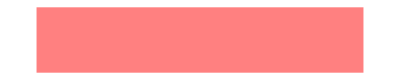

```mathematica
ppPlotCoulbournElement[tempTrial[[1]],Pink]
```

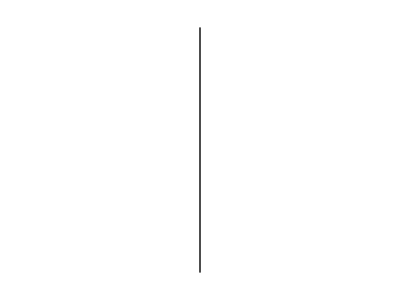

```mathematica
ppPlotCoulbournElement[tempTrial[[2]],Black]
```

```mathematica
ppCoulbournTrialType[tempTrial]
```

GO

```mathematica
FirstCase[tempTrial,{"Coulbourn",_,_,x_/;MemberQ[{4,7,10},x],___}]
```

{Coulbourn,0.,0.,4,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).,Sw2}

```mathematica
FirstCase[tempTrial,{"Coulbourn",_,_,x_/;MemberQ[{4,7,10}+10,x],___}][[0]]===Missing
```

True

```mathematica
ppCoulbournTrialType[trial_List]:=
Module[{tempStim},
tempStim=FirstCase[trial,{"Coulbourn",_,_,x_/;MemberQ[{4,7,10},x],___}];
If[tempStim[[0]]===Missing,  
Message[ppCoulbournTrialType::noTrialTrigger, trial]; Null,
Switch[tempStim[[4]],4,"GO", 7,"NOGO", 10,"TEST"]
]
];
ppCoulbournTrialType::noTrialTrigger="Input `1` does not contain a trial trigger!";
```

```mathematica
ppPlotCoulbournElement[trialElement_List, color_/;ColorQ[color]]:=
Graphics[{
color,
If[trialElement[[3]]==0,
Line[{{trialElement[[2]],-1},{trialElement[[2]],1}}],
Rectangle[{-1,trialElement[[2]]},{1,trialElement[[2]]+trialElement[[3]]}]
]
}
];
```

```mathematica
ppPlotCoulbournStimulus[trial_List]:=
Module[{tempTrialStim},
tempTrialStim=Select[tempTrial, #[[1]]==="Stimulus"&];
Graphics[{
Switch[ppCoulbournTrialType[trial],"GO"Opacity[0.25, ColorData["HTML"]["DarkOliveGreen"]],Opacity[0.25,ColorData["HTML"]["DarkRed"]]],
Rectangle[{-1,trial[[2]]},{1,trial[[2]]+trial[[3]]}]}
]
]
```

```mathematica
ppPlotCoulbournTrial[trial_List]:=
Module[{tempEntry,tempTrial, tempStimulus,tempTrialType},
tempEntry=SelectFirst[trial,MemberQ[{4,7,10},#[[4]]]&][[2]];

tempTrial=ReplacePart[#, {2->(#[[2]]-tempEntry)/1000000.,3->#[[3]]/1000000. }]& /@ trial;
tempTrialType=ppCoulbournTrialType[tempTrial];
tempStimulus=FirstCase[tempTrial,{"Stimulus",___}]; tempTrial= Cases[tempTrial, Except[tempStimulus]];
(*tempJumpEscape=
tempJumpEntry=
tempJumpRandom=*)

Show[
Graphics[
{},
Axes->{True,None},AxesOrigin->{0,0},
PlotRange->{{-5,30},{-1.1,1}}],
ppPlotCoulbournElement[tempStimulus,Switch[tempTrialType,"GO",Opacity[0.25, ColorData["HTML"]["DarkOliveGreen"]],"NOGO",Opacity[0.25,ColorData["HTML"]["DarkRed"]],"TEST",Opacity[0.25,Black]]]
]
]
```

```mathematica
s
```

False

```mathematica
ppPlotCoulbournTrial[trialsCoulb[[1]]]
```

Show::gcomb: Could not combine the graphics objects in GraphicsBox[List[], Rule[Axes, List[True, None]], Rule[AxesOrigin, List[0, 0]], Rule[PlotRange, List[List[-5, 30], List[-1.1`, 1]]]], ppPlotCoulbournElement[{.

Show[-Graphics-,ppPlotCoulbournElement[{Stimulus,-0.019375,0.016718,1,TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).,XXX},Opacity[0.25,-Graphics-]]]

## Import Video and Align